Seesaw method for the Clifford MoE game
Author: Ion Nechita

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
```

```mathematica
(*Generates the Clifford elements up to K=19*)
spinSystem[k_]:=Module[{A,B,C,d},
If[k<=3,
Return[Table[PauliMatrix[i],{i,1,k}]]];
If[4<=k&&k<=5,
A=spinSystem[3];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,3}];
C=Table[KroneckerProduct[PauliMatrix[i-2],IdentityMatrix[d]],{i,4,k}];
Return[Join[B,C]];
];
If[6<=k&&k<=7,
A=spinSystem[5];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,5}];
C=Table[KroneckerProduct[PauliMatrix[i-4],IdentityMatrix[d]],{i,6,k}];
Return[Join[B,C]];
];
If[8<=k&&k<=9,
A=spinSystem[7];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,7}];
C=Table[KroneckerProduct[PauliMatrix[i-6],IdentityMatrix[d]],{i,8,k}];
Return[Join[B,C]];
];
If[10<=k&&k<=11,
A=spinSystem[9];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,9}];
C=Table[KroneckerProduct[PauliMatrix[i-8],IdentityMatrix[d]],{i,10,k}];
Return[Join[B,C]];
];
If[12<=k&&k<=13,
A=spinSystem[11];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,11}];
C=Table[KroneckerProduct[PauliMatrix[i-10],IdentityMatrix[d]],{i,12,k}];
Return[Join[B,C]];
];
If[14<=k&&k<=15,
A=spinSystem[13];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,13}];
C=Table[KroneckerProduct[PauliMatrix[i-12],IdentityMatrix[d]],{i,14,k}];
Return[Join[B,C]];
];
If[16<=k&&k<=17,
A=spinSystem[15];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,15}];
C=Table[KroneckerProduct[PauliMatrix[i-14],IdentityMatrix[d]],{i,16,k}];
Return[Join[B,C]];
];
If[18<=k&&k<=19,
A=spinSystem[17];
d=Dimensions[A][[2]];
B=Table[KroneckerProduct[PauliMatrix[1],A[[i]]],{i,1,17}];
C=Table[KroneckerProduct[PauliMatrix[i-16],IdentityMatrix[d]],{i,18,k}];
Return[Join[B,C]];
];
Return[{}];
];
```

```mathematica
(*Helper function producing a Haar-distributed random projection of rank r in M_d, used to initialize the see-saw algorithm*)
randomProjection[d_,r_]:=Module[{U,V},
U=RandomVariate[CircularUnitaryMatrixDistribution[d]];
V=U[[;;,1;;r]];
V.ConjugateTranspose[V]
]
```

```mathematica
(*
This is the main function which uses the see-saw algorithm to find interesting feasible points for the optimization problem from Eq. (11) and Conjecture 1 in the paper. 

We succesively optimizer over the following 3 paramters: 
- z, a vector which attains the operator norm in (11)
- the matrices B (of operator norm <=1)
- the matrices C (of operator norm <=1)

The input paramters are:
- the matrices A (which are fixed, and we take them to be the Clifford elements in our scheme)
- the dimensions dimB and dimC of the matrices B and C (which are free in Conjecture 1)
- the number of iterations we let our see-saw algorithm to run

The algorithm follows the  discussion in Sec 4.4. of the paper.
*)
alternatingOptimization[A_,dimB_,dimC_,nIter_]:=Module[{K,dimA,B,C,x,z,cost,M,z213,R,S,iter,vals,vecs,z312,i,v1,v2,v3},
K=Dimensions[A][[1]];
dimA=Dimensions[A][[2]];
B=ConstantArray[0,{K,dimB,dimB}];
For[x=1,x<=K,x++,
B[[x]]=2randomProjection[dimB,Floor[dimB/2]]-IdentityMatrix[dimB];
];
C=ConstantArray[0,{K,dimC,dimC}];
For[x=1,x<=K,x++,
C[[x]]=2randomProjection[dimC,Floor[dimC/2]]-IdentityMatrix[dimC];
];
cost={};
For[iter=1,iter<=nIter,iter++,
(*optimize over z*)
M=ConstantArray[0,{dimA dimB dimC,dimA dimB dimC}];
For[x=1,x<=K,x++,
M=M+KroneckerProduct[A[[x]],KroneckerProduct[B[[x]],IdentityMatrix[dimC]]]+
KroneckerProduct[A[[x]],KroneckerProduct[IdentityMatrix[dimB],C[[x]]]]+
KroneckerProduct[IdentityMatrix[dimA],KroneckerProduct[B[[x]],C[[x]]]];
];
M=(M+ConjugateTranspose[M])/2;
{vals,vecs}=Eigensystem[M];
i=Ordering[vals,-1];
z=Transpose[vecs[[i]]];
AppendTo[cost,Re[(ConjugateTranspose[z].M.z)[[1,1]]]];
(*Print[SingularValueList[ArrayReshape[z,{dimA,dimB dimC}]]^2];*)
(*optimize over B*)
For[x=1,x<=K,x++,
R=KroneckerProduct[A[[x]],IdentityMatrix[dimC]]+
KroneckerProduct[IdentityMatrix[dimA],C[[x]]];
v1=Re[(ConjugateTranspose[z].(KroneckerProduct[A[[x]],KroneckerProduct[B[[x]],IdentityMatrix[dimC]]]+
KroneckerProduct[A[[x]],KroneckerProduct[IdentityMatrix[dimB],C[[x]]]]+
KroneckerProduct[IdentityMatrix[dimA],KroneckerProduct[B[[x]],C[[x]]]]).z)[[1,1]]];
z213=ArrayReshape[z,{dimA,dimB,dimC}];
z213=Transpose[z213,{2,1,3}];
z213=ArrayReshape[Flatten[z213],{dimB,dimA dimC}];
S=z213.Transpose[R].ConjugateTranspose[z213];
S=(S+ConjugateTranspose[S])/2;
v2=Tr[B[[x]].S]//Re;
{vals,vecs}=Eigensystem[S];
(*Print[vals];*)
vals=Sign[vals];
B[[x]]=Transpose[vecs].DiagonalMatrix[vals].Conjugate[vecs];
v3=Re[(ConjugateTranspose[z].KroneckerProduct[B[[x]],R].z)[[1,1]]];
(*Print[v1," --- ",v2," --- ",v3];*)
(*Print[Eigenvalues[R],Eigenvalues[B[[x]]]];*)
];
M=ConstantArray[0,{dimA dimB dimC,dimA dimB dimC}];
For[x=1,x<=K,x++,
M=M+KroneckerProduct[A[[x]],KroneckerProduct[B[[x]],IdentityMatrix[dimC]]]+
KroneckerProduct[A[[x]],KroneckerProduct[IdentityMatrix[dimB],C[[x]]]]+
KroneckerProduct[IdentityMatrix[dimA],KroneckerProduct[B[[x]],C[[x]]]];
];
M=(M+ConjugateTranspose[M])/2;
AppendTo[cost,Re[(ConjugateTranspose[z].M.z)[[1,1]]]];
(*optimize over C*)
For[x=1,x<=K,x++,
R=KroneckerProduct[A[[x]],IdentityMatrix[dimB]]+
KroneckerProduct[IdentityMatrix[dimA],B[[x]]];
v1=Re[(ConjugateTranspose[z].KroneckerProduct[R,C[[x]]].z)[[1,1]]];
z312=Transpose[ArrayReshape[z,{dimA dimB,dimC}]];
S=z312.Transpose[R].ConjugateTranspose[z312];
S=(S+ConjugateTranspose[S])/2;
v2=Tr[C[[x]].S]//Re;
{vals,vecs}=Eigensystem[S];
(*Print[vals];*)
vals=Sign[vals];
C[[x]]=Transpose[vecs].DiagonalMatrix[vals].Conjugate[vecs];
v3=Re[(ConjugateTranspose[z].KroneckerProduct[R,C[[x]]].z)[[1,1]]];
(*Print[v1," --- ",v2," --- ",v3];*)
(*Print[Eigenvalues[R],Eigenvalues[C[[x]]]];*)
];
M=ConstantArray[0,{dimA dimB dimC,dimA dimB dimC}];
For[x=1,x<=K,x++,
M=M+KroneckerProduct[A[[x]],KroneckerProduct[B[[x]],IdentityMatrix[dimC]]]+
KroneckerProduct[A[[x]],KroneckerProduct[IdentityMatrix[dimB],C[[x]]]]+
KroneckerProduct[IdentityMatrix[dimA],KroneckerProduct[B[[x]],C[[x]]]];
];
M=(M+ConjugateTranspose[M])/2;
AppendTo[cost,Re[(ConjugateTranspose[z].M.z)[[1,1]]]];
];
cost
];
```

```mathematica
(*We generate the values for K=3 and dimB=dimC=2,4,8, with Niter=1000 iterations of the see-saw algorithm, ran M=10 times for each value*)
K=3;
M=10;
Niter=100;
A=spinSystem[K];
dimBC=2;
cost=ConstantArray[0,{Niter,3M}];
For[i=1,i<=Niter,i++,cost[[i,;;]]=alternatingOptimization[A,dimBC,dimBC,M]];
cost2=Log[cost/(K+2Sqrt[K])];
dimBC=4;
cost=ConstantArray[0,{Niter,3M}];
For[i=1,i<=Niter,i++,cost[[i,;;]]=alternatingOptimization[A,dimBC,dimBC,M]];
cost4=Log[cost/(K+2Sqrt[K])];
dimBC=8;
cost=ConstantArray[0,{Niter,3M}];
For[i=1,i<=Niter,i++,cost[[i,;;]]=alternatingOptimization[A,dimBC,dimBC,M]];
cost8=Log[cost/(K+2Sqrt[K])];
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

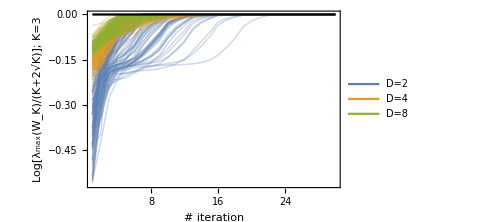

```mathematica
(*We plot the 3xM curves, on a log scale, along with the conjectured upper bound of 0*)
colors=ColorData[97,"ColorList"]
op=0.3;
th=0.003;
Show[
ListLinePlot[Join[Table[cost2[[i,;;]],{i,1,Niter}],Table[cost4[[i,;;]],{i,1,Niter}],Table[cost8[[i,;;]],{i,1,Niter}],{Table[0,3M]}],PlotRange->{{1,30},All},PlotStyle->Join[Table[{colors[[1]],Opacity[op],Thickness[th]},Niter],Table[{colors[[2]],Opacity[op],Thickness[th]},Niter],Table[{colors[[3]],Opacity[op],Thickness[th]},Niter],{{Black}}],Frame->True,FrameLabel->{"# iteration","Log[λ_max(W_K)/(K+2√K)]; K=3"},PlotLegends->Placed[LineLegend[{colors[[1]],colors[[2]],colors[[3]]},{"D=2","D=4","D=8"}],{0.85,0.25}],ImageSize->Medium]]
Export["K3-seesaw.png",%,ImageResolution->1000]
```